{{x[1,1]→0,x[1,2]→0,x[2,1]→0,x[2,2]→0,y[1,1]→0,y[1,2]→-1,y[2,1]→-1,y[2,2]→0,z[1,1]→0,z[1,2]→1,z[2,1]→1,z[2,2]→0,w[1,1]→0,w[1,2]→0,w[2,1]→0,w[2,2]→0,a[1,1]→0,a[1,2]→0,a[1,3]→0,a[1,4]→-1,a[2,1]→0,a[2,2]→0,a[2,3]→-1,a[2,4]→0,a[3,1]→1,a[3,2]→0,a[3,3]→0,a[3,4]→0,a[4,1]→0,a[4,2]→1,a[4,3]→0,a[4,4]→0}}

(2. Δ+O[1/Δ]^2 | 0. | 0. | 0.
0. | 2. Δ+O[1/Δ]^2 | 0. | 0.
0. | 0. | 2. Δ+O[1/Δ]^2 | 0.
0. | 0. | 0. | 2. Δ+O[1/Δ]^2)

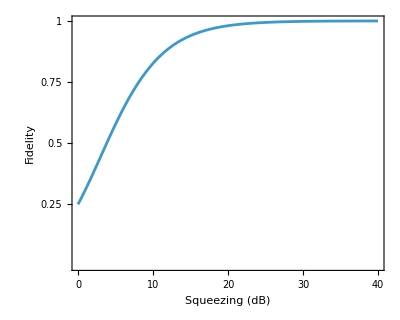

(1 | 1
1 | 2)

```mathematica
(*Define Cluster State Matrix A as four 2x2 blocks*)
Bmat={{0,0},{0,0}};
Cmat={{0,1},{1,0}};
CITmat=Transpose[Inverse[Cmat]];
Dmat={{0,0},{0,0}};
Amat=ArrayFlatten[{{Bmat,Cmat},{Transpose[Cmat],Dmat}}];
I4= IdentityMatrix[4];
I2 = IdentityMatrix[2];
O2 = ConstantArray[0,{2,2}];
O4=ConstantArray[0,{4,4}];
Omega=ArrayFlatten[{{O4,I4},{-I4,O4}}];
Normmat=MatrixPower[IdentityMatrix[4]+MatrixPower[Amat,2],-1/2];
InitialO= N[ArrayFlatten[{{Normmat.I4, Normmat.Amat},{-Normmat.Amat,Normmat.I4}}]];
Clear[Δ];
Squeezing=Δ;
InitialEigen = DiagonalMatrix[{1/Squeezing,1/Squeezing,1/Squeezing,1/Squeezing,Squeezing,Squeezing,Squeezing,Squeezing}];
InitialCov = Transpose[InitialO].InitialEigen.InitialO;
quad1={1,0,-1,0,0,0,0,0};
quad2={0,1,0,-1,0,0,0,0};
quad3={0,0,0,0,1,0,1,0};
quad4={0,0,0,0,0,1,0,1};
quads={quad1,quad2,quad3,quad4};
puad1={1,0,1,0,0,0,0,0};
puad2={0,1,0,1,0,0,0,0};
puad3={0,0,0,0,1,0,-1,0};
puad4={0,0,0,0,0,1,0,-1};
puads={puad1,puad2,puad3,puad4};
PTx=Array[x,{2,2}];
PTy=Array[y,{2,2}];
PTz=Array[z,{2,2}];
PTw=Array[w,{2,2}];
SolvePT=ArrayFlatten[{{PTx,O2,PTy,O2},{O2,I2,O2,O2},{PTz,O2,PTw,O2},{O2,O2,O2,I2}}];
SolveAnc=Array[a,{4,4}];
equations2=Flatten[SolveAnc.puads==ArrayFlatten[{{I4,Amat}}].SolvePT];

(*Solve for the unknowns*)
sol=Solve[{equations2},Flatten[{PTx,PTy,PTz,PTw,SolveAnc}]]
PTxSolved=PTx/. sol[[1]];
PTySolved=PTy/. sol[[1]];
PTzSolved=PTz/. sol[[1]];
PTwSolved=PTw/. sol[[1]];
PTSolved=ArrayFlatten[{{PTxSolved,O2,PTySolved,O2},{O2,I2,O2,O2},{PTzSolved,O2,PTwSolved,O2},{O2,O2,O2,I2}}];
TrueFinalCov=Transpose[PTSolved].InitialCov.PTSolved;
TrueReducedCov=quads.TrueFinalCov.Transpose[quads];
Series[TrueReducedCov,{Δ,Infinity,1}]//MatrixForm
ticks={{0.25,Style["0.25",12]},{0.5,Style["0.5",12]},{0.75,Style["0.75",12]},{1,Style["1",12]}};
p=ParametricPlot[
{-10Log[10,Δ],Evaluate[4/Sqrt[Det[2I4+TrueReducedCov]]]},
{Δ,0.0001,1},
FrameLabel->{Style["Squeezing (dB)",22],Style["Fidelity",22]},
Frame->True,
GridLines->None,
PlotRange->{{0,40},{0,1}},
AspectRatio->0.8,
FrameTicks->{{ticks,None},{Automatic,Automatic}},
FrameTicksStyle->12
]
```

```mathematica
Information[Amat]
```

Information[ArrayFlatten[{{{{1,1},{1,2}},{{1,1},{3,4}}}},{{{{1,3},{1,4}},{{6,10},{10,20}}}}]]

```mathematica
Information[A]
```

Information[ArrayFlatten[{{{{1,1},{1,2}},C}},{{Transpose[C],D}}]]